## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p375/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
saveFolderLT="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p380/";
```

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031 };
```

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 };
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000}

```mathematica
wtlist={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{0.00,50000.00,60000.00,70000.00,80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.7500_T",Tstring[[7]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.7500_T",Tstring[[7]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,7}],{idx,0,2}];
```

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.7500_T",Tstring[[7]],"_waitingTime",wtliststring[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,7}];
```

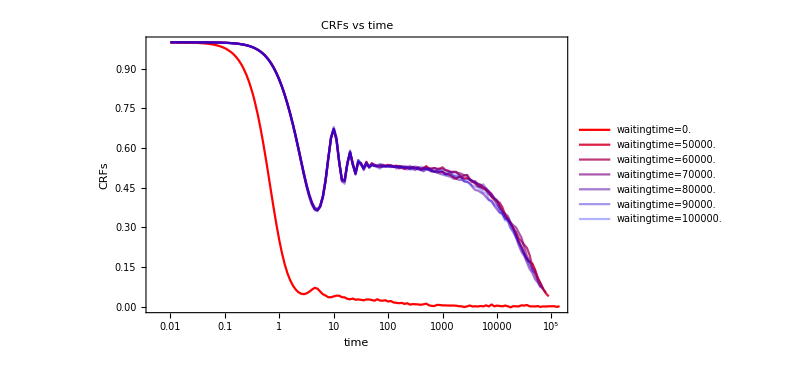

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISF[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,7}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,7}],PlotRange->All]
```

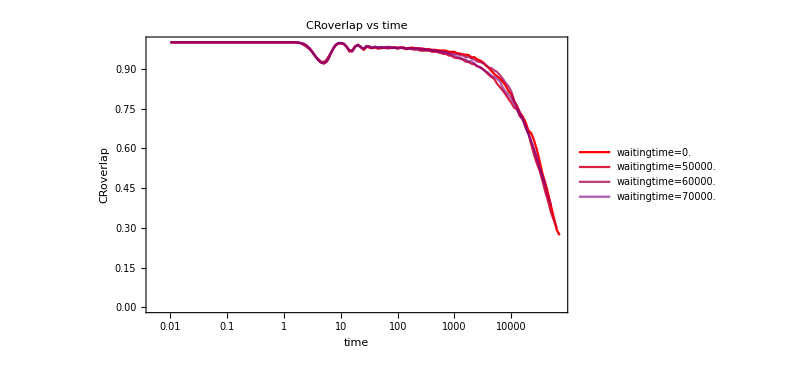

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]}],{wt,4,7}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,7}],PlotRange->{All,{0,1}}]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.7500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Length[Tlist]
```

11

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.7500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Length[overlap[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Length[SISF[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Length[SISF[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.7500_T",Tstring[[7]],"_waitingTime",wtlistLongestString[[7]],"_idx1.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7}

```mathematica
Log10[timeLongest[[52]]]
```

1.80003

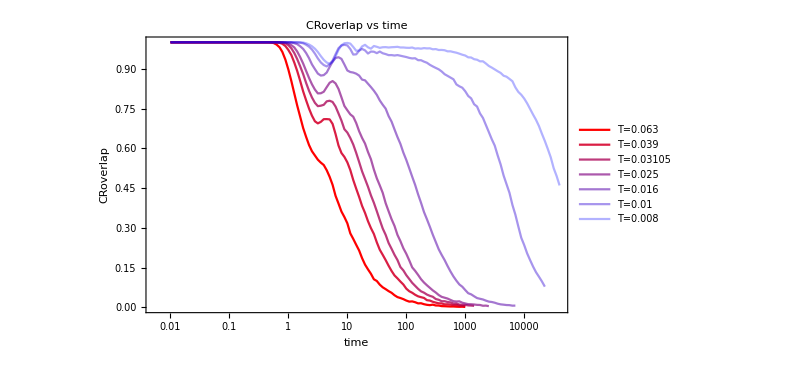

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartNum={5.412414221286025,10.105967590338425,12.838602823758816,16.306676432777856,24.035701100947822,48.32603339781185,60.24027351376765};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{46,52,54,56,59,65,67}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitCROverlapStartPos[[T]],Length[CRoverlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.989978 ⅇ^(-0.295338 t^0.590253)],FittedModel[0.989987 ⅇ^(-0.159244 t^0.617099)],FittedModel[0.989992 ⅇ^(-0.103578 t^0.652423)],FittedModel[0.989994 ⅇ^(-0.0670837 t^0.680868)],FittedModel[0.989998 ⅇ^(-0.0176002 t^0.753084)],FittedModel[0.962474 ⅇ^(-0.000313918 t^0.908774)],FittedModel[0.982364 ⅇ^(-0.0000773052 t^0.86627)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{7.89548,19.6357,32.3109,52.8886,213.664,7158.94,55789.1}

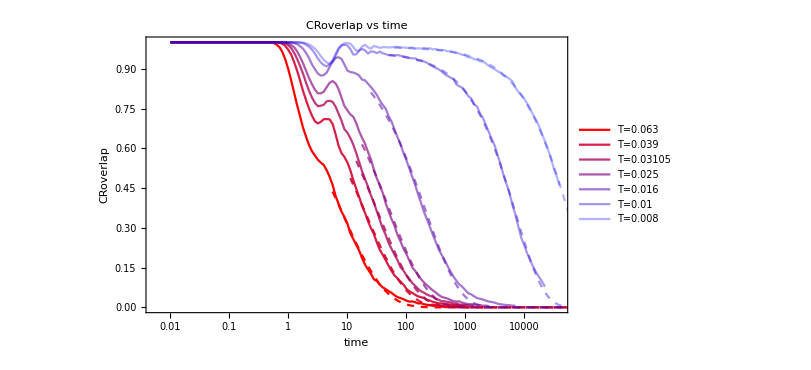

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

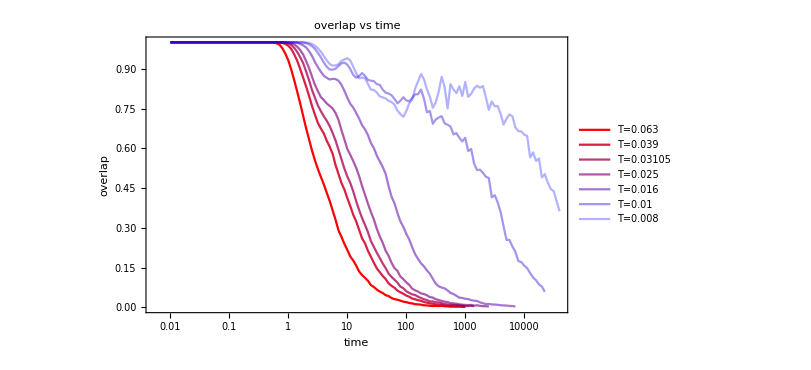

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
fitOverlapStartNum={2.7441689315428452,4.928152330342358,6.4852176223676565,8.69205616928665,19.81094288120914,277.0419227275217,909.6317348902828};
```

```mathematica
fitOverlapStartPos=Table[Position[time,_?(#>fitOverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{40,45,48,50,57,80,91}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.9>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.899994 ⅇ^(-0.265912 t^0.697059)],FittedModel[0.899996 ⅇ^(-0.148386 t^0.712341)],FittedModel[0.899995 ⅇ^(-0.125101 t^0.696903)],FittedModel[0.899996 ⅇ^(-0.0807895 t^0.738576)],FittedModel[0.899998 ⅇ^(-0.0413426 t^0.710072)],FittedModel[0.826234 ⅇ^(-0.00195926 t^0.732076)],FittedModel[0.894728 ⅇ^(-0.000642567 t^0.681296)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{6.68761,14.5619,19.7405,30.1575,88.8258,4999.69,48451.5}

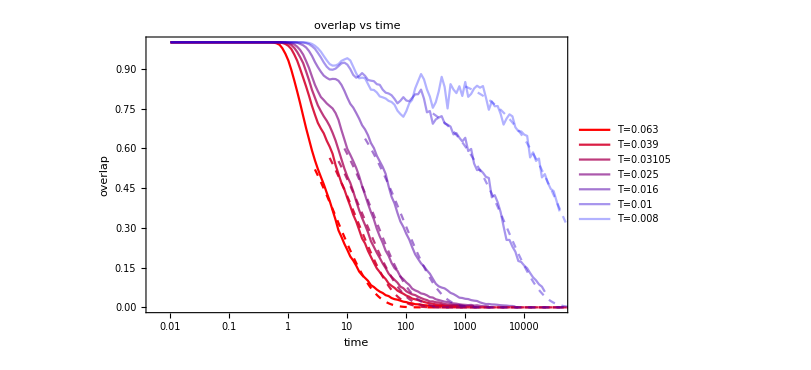

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

#### CRSISF

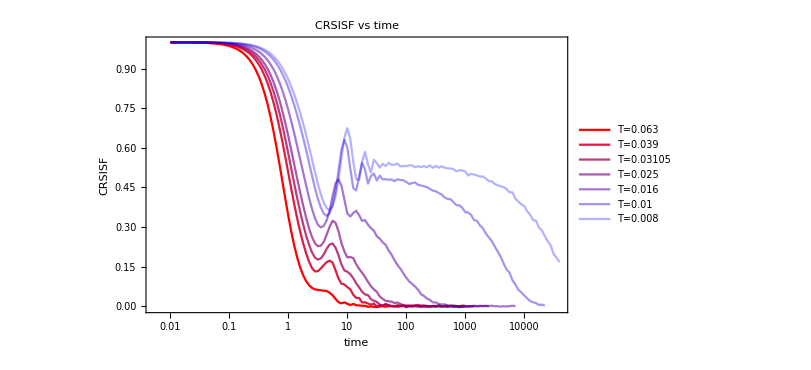

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={8.6492291451835,8.81855496486187,11.19985714692304,13.460931876894174,22.545863663284553,47.93826585170533,55.56550431632648};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{50,50,52,54,59,65,66}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.349106 ⅇ^(-0.584987 t^0.785673)],FittedModel[0.518608 ⅇ^(-0.278876 t^0.855193)],FittedModel[0.56973 ⅇ^(-0.199931 t^0.845837)],FittedModel[0.597178 ⅇ^(-0.170394 t^0.771312)],FittedModel[0.481856 ⅇ^(-0.0358214 t^0.805199)],FittedModel[0.486015 ⅇ^(-0.000574459 t^0.899978)],FittedModel[0.536044 ⅇ^(-0.000141338 t^0.851014)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{1.97868,4.4514,6.70722,9.91777,62.4671,3989.43,33397.1}

```mathematica
Length[TlistLongest]
```

5

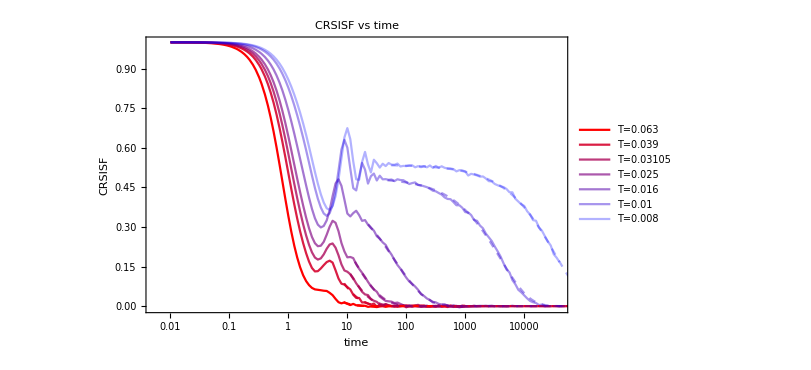

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

#### SISF

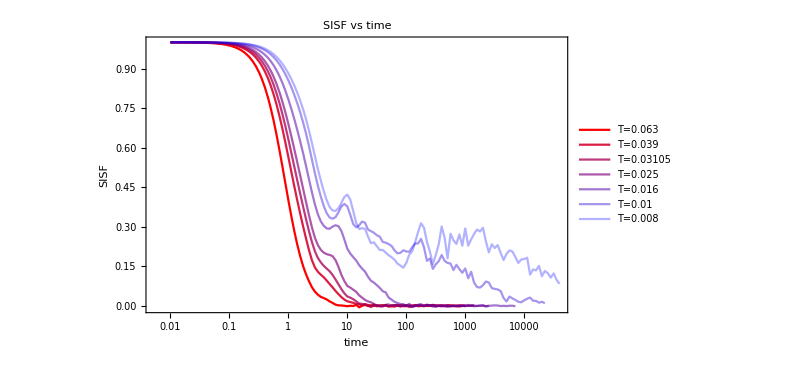

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

```mathematica
time[[54]]
```

14.13

```mathematica
fitSISFStartPos={45,50,52,54,59,85,85}
```

{45,50,52,54,59,85,85}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.5>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsSISF
```

{FittedModel[0.389695 ⅇ^(-1.21686 t^0.84734)],FittedModel[0.471656 ⅇ^(-0.667003 t^0.87804)],FittedModel[0.475772 ⅇ^(-0.590409 t^0.769207)],FittedModel[0.492489 ⅇ^(-0.36901 t^0.862963)],FittedModel[0.401057 ⅇ^(-0.192664 t^0.896631)],FittedModel[0.496577 ⅇ^(-0.122052 t^0.897377)],FittedModel[0.294387 ⅇ^(-0.0722042 t^0.894352)],FittedModel[0.499604 ⅇ^(-0.06711 t^0.899403)],FittedModel[0.363914 ⅇ^(-0.0360303 t^0.898127)],FittedModel[0.192066 ⅇ^(-0.0290289 t^0.742003)],FittedModel[0.191781 ⅇ^(-0.0249584 t^0.680195)],FittedModel[0.146665 ⅇ^(-0.00995751 t^0.755348)],FittedModel[0.115751 ⅇ^(-0.00128434 t^0.899582)],FittedModel[0.210123 ⅇ^(-0.00352549 t^0.746696)],FittedModel[0.183986 ⅇ^(-0.00355128 t^0.688254)],FittedModel[0.219591 ⅇ^(-0.00369183 t^0.656228)]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{1.2259,2.21763,3.58791,5.68334,19.2413,378.721,29896.3}

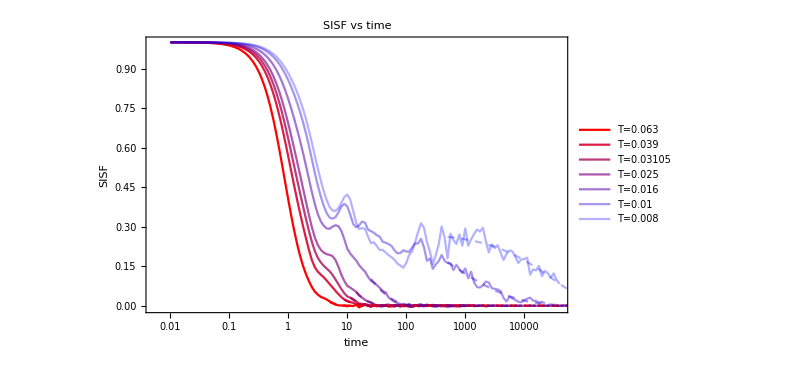

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

#### Tau Alphas

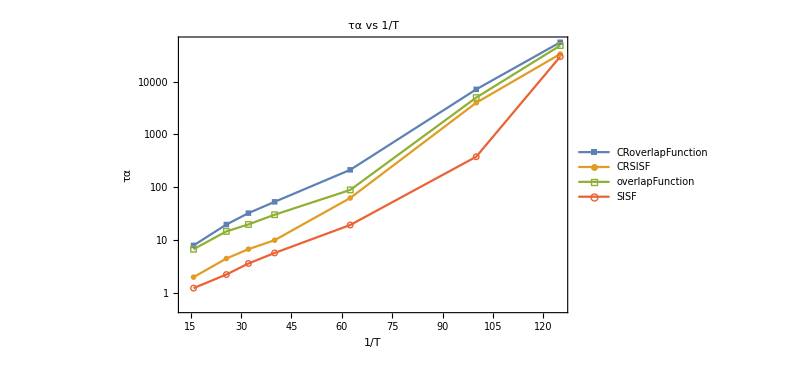

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCROverlapfits[[T]],tauCRSISFfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,7.89548,1.97868,6.68761,1.2259},{0.039,19.6357,4.4514,14.5619,2.21763},{0.03105,32.3109,6.70722,19.7405,3.58791},{0.025,52.8886,9.91777,30.1575,5.68334},{0.016,213.664,62.4671,88.8258,19.2413},{0.01,7158.94,3989.43,4999.69,378.721},{0.008,55789.1,33397.1,48451.5,29896.3}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP375.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP375.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p380.jpeg",tauAlphafitingPlot];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.809979,0.796758,0.809037,0.809862,0.80979,0.809928,0.80995,0.809939,0.809968,0.80997,0.809986,0.809967,0.809928,0.703551,0.771414,0.809972,0.809195,0.809984,0.793789,0.809994,0.809994,0.809994,0.794059}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.449978,0.437055,0.448006,0.449785,0.449754,0.449922,0.449957,0.449934,0.449975,0.449977,0.44999,0.449993,0.441588,0.473171,0.454078,0.449017,0.44834,0.455473,0.448606,0.457386,0.45083,0.452285,0.449566}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

{0.529141,0.592079,0.569808,0.630995,0.641043,0.665991,0.691322,0.701875,0.704992,0.729689,0.738498,0.762204,0.759353,0.730815,0.74279,0.794476,0.764024,0.795187,0.765277,0.801778,0.865234,0.912167,0.836894}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

{0.999912,0.999974,0.999974,0.999988,0.999992,0.999993,0.999996,0.999996,0.999997,0.999996,0.999997,0.999998,0.980185,0.993608,0.988459,0.976593,0.980814,0.978599,0.973606,0.976955,0.965694,0.961696,0.962681}

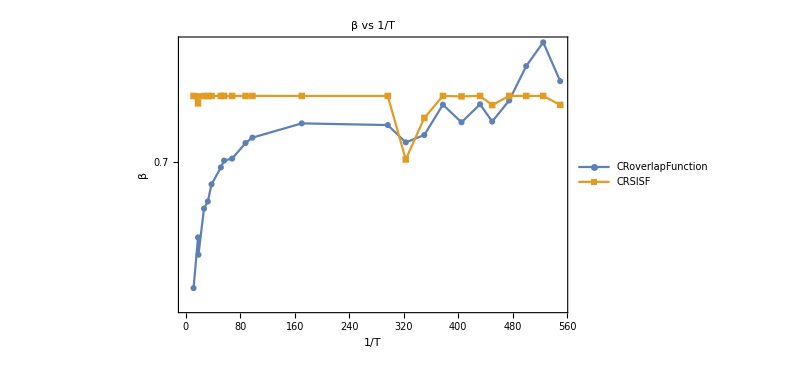

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

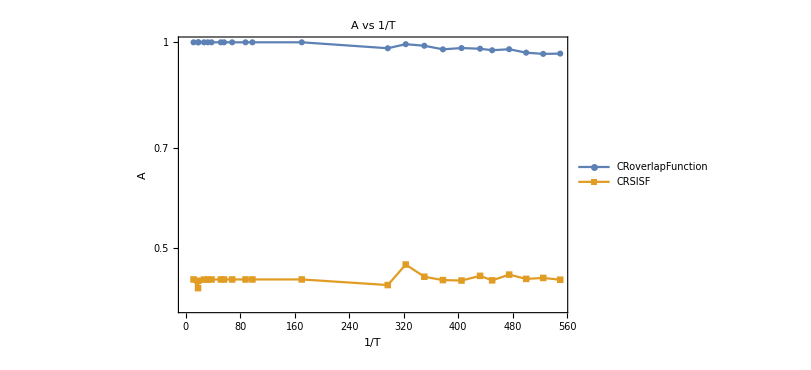

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

{0.728537,1.41524,1.61389,2.6929,4.03698,5.21129,9.19522,9.51448,14.8936,25.9793,32.3344,138.256,1036.02,1239.22,2019.54,2804.8,4144.73,5262.53,6834.04,9346.07,13224.1,18754.3,19569.1}

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap},{0.08868,0.728537,3.16039},{0.05586,1.41524,6.7635},{0.05409,1.61389,6.75448},{0.03756,2.6929,12.5106},{0.03105,4.03698,17.4891},{0.02652,5.21129,23.0389},{0.01945,9.19522,38.8819},{0.01782,9.51448,42.9591},{0.01471,14.8936,64.5399},{0.01141,25.9793,101.84},{0.01023,32.3344,125.531},{0.005873,138.256,436.846},{0.003371,1036.02,2732.95},{0.00309559,1239.22,3582.02},{0.00285428,2019.54,5140.15},{0.00264787,2804.8,7160.55},{0.00246931,4144.73,10064.4},{0.0023133,5262.53,13246.9},{0.00222222,6834.04,17008.4},{0.00210526,9346.07,22594.2},{0.002,13224.1,29109.1},{0.00190476,18754.3,39352.1},{0.00181818,19569.1,46020.2}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

{0.088680,0.055860,0.054090,0.037560,0.031050,0.026520,0.019450,0.017820,0.014710,0.011410,0.010230,0.005873,0.003371,0.003096,0.002854,0.002648,0.002469,0.002313,0.002222,0.002105,0.002000,0.001905,0.001818}

```mathematica
TlistAllT
```

{0.08868,0.05586,0.05409,0.03756,0.03105,0.02652,0.01945,0.01782,0.01471,0.01141,0.01023,0.005873,0.003371,0.00309559,0.00285428,0.00264787,0.00246931,0.0023133,0.00222222,0.00210526,0.002,0.00190476,0.00181818}

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

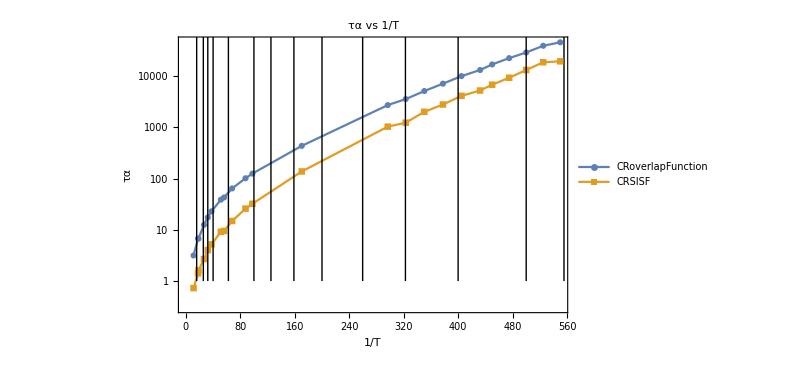

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

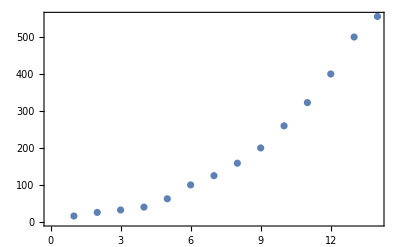

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16